```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bedfordt/Documents/current-projects/coalescent-inference/coalescent-toolbox

## Simple tree

```mathematica
{tips,trunk,rules,labels,coords}=Import["rules.txt","Table"];
```

```mathematica
rules=ToExpression[rules];labels=ToExpression[labels];coords=ToExpression[coords];
```

```mathematica
n=Length[Union[labels[[All,2]]]];
```

```mathematica
colorlist=If[n>1,Table[ColorData["Rainbow"][(i-1)/(n-1)],{i,n}],{ColorData["Rainbow"][1]}];
```

```mathematica
colorrules=Map[#->ColorData["Rainbow"][(#-1)/n]&,Union[labels[[All,2]]]];
```

```mathematica
Grid[{Map[Graphics[{#/.colorrules,Text[#,{0,0}]},ImageSize->{20,20}]&,colorrules[[All,1]]]}]
```

-Graphics-

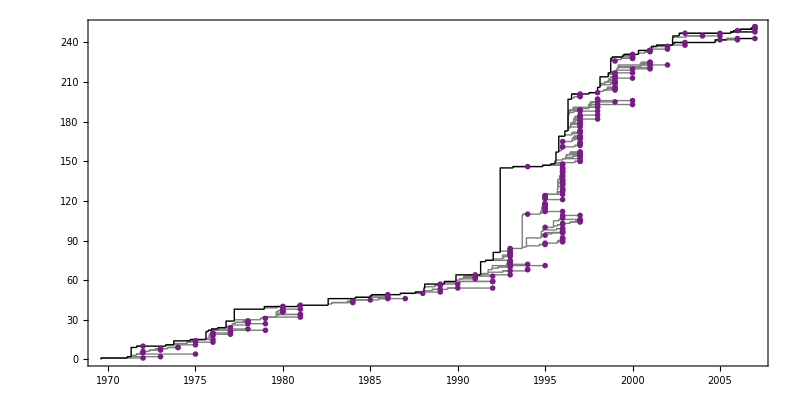

```mathematica
Graphics[{Map[{If[MemberQ[trunk,#[[1]]],Black,Gray],With[{coordsA=#[[1]]/.coords,coordsB=#[[2]]/.coords},Line[{coordsA,{coordsB[[1]],coordsA[[2]]},coordsB}]]}&,rules],{PointSize[0.005],Map[{#/.labels/.colorrules,Point[(#/.coords)]}&,tips]}},ImageSize->800,AspectRatio->0.5,Frame->{True,False,False,False}]
```

Colored edges.

Graphics[{Map[{colorlist[[#[[1]] /. labels]], With[{coordsA = #[[1]] /. coords, coordsB = #[[2]] /. coords}, Line[{coordsA, {coordsB[[1]], coordsA[[2]]}, coordsB}]]} &, rules], {PointSize[0.005], Map[{colorlist[[# /. labels]], Point[(# /. coords)]} &, tips]}}, ImageSize -> 800, AspectRatio -> 0.5, Frame -> {True, False, False, False}]

## Padded Tree

```mathematica
Options[evolPlot]={ImageSize->Medium,AspectRatio->0.7};
```

```mathematica
evolPlot[rules_,times_]:=Module[{lcount},
lcount=Length[Gather[labels[[All,2]]]];
TreePlot[rules,Left,0,
EdgeRenderingFunction->({If[MemberQ[trunk,#2[[1]]],Black,Gray],If[MemberQ[trunk,#2[[1]]],Thickness[0.0008],{}],Line[{#1[[1]],{#1[[2,1]],#1[[1,2]]},#1[[2]]}]}&),
VertexRenderingFunction->(If[#2≤count&&#2>0,
{PointSize[0.003],Point[#1]},{}]&),
LayerSizeFunction->(Reverse[Differences[times]][[#]]&),
ImageSize->800,AspectRatio->0.5]]
```

```mathematica
{count,ends,trunk,rules,times}=Import["paddedrules.txt","Table"];
```

```mathematica
count=First[count];rules=ToExpression[rules];
```

Part::partd: Part specification {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 1814 »} ⟦ All, 2 ⟧ is longer than depth of object.

Gather::list: List expected at position 1 in Gather[{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 1814 »} ⟦ All, 2 ⟧].

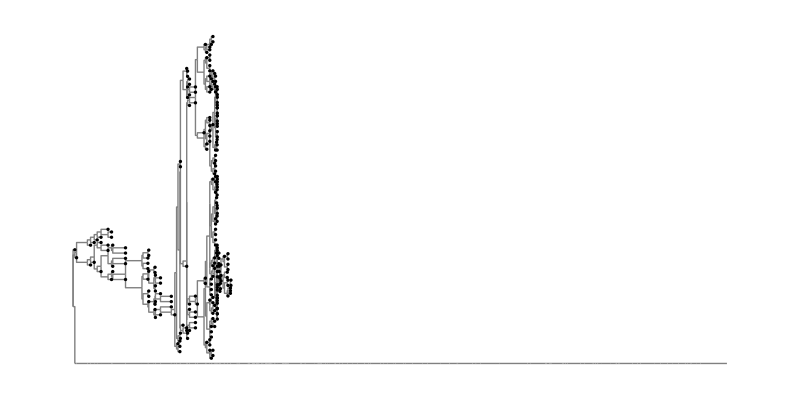

```mathematica
evolPlot[rules,times]
```

## Skyline plots

### TMRCA

```mathematica
skl=Import["tmrca.skl","Table"];
```

```mathematica
mean=Map[{2008-#[[1]],#[[2]]}&,skl];
```

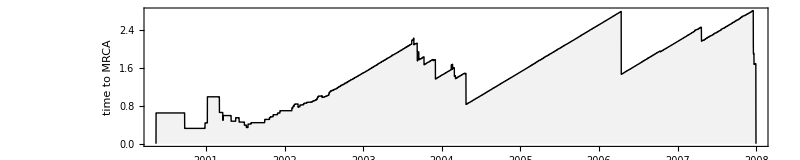

```mathematica
ListLinePlot[mean,PlotRange->{{2002,2007},{0,All}},Frame->{True,True,False,False},Axes->False,AspectRatio->0.2,ImageSize->800,Filling->Axis,FrameLabel->{"","time to MRCA"},PlotStyle->Black,FillingStyle->Directive[Opacity[0.1],GrayLevel[0.5]]]
```

### Diversity

```mathematica
skl=Import["div_6dr.skl","Table"];
```

```mathematica
mean=Map[{2008-#[[1]],#[[2]]}&,skl];
```

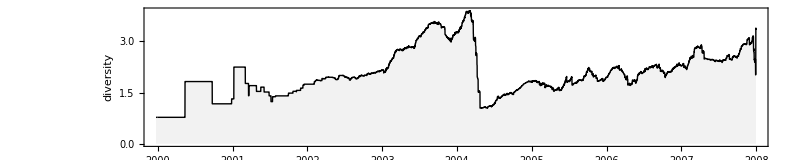

```mathematica
ListLinePlot[mean,PlotRange->{{2002,2007},{0,All}},Frame->{True,True,False,False},Axes->False,AspectRatio->0.2,ImageSize->800,Filling->Axis,FrameLabel->{"","diversity"},PlotStyle->Black,FillingStyle->Directive[Opacity[0.1],GrayLevel[0.5]]]
```